```mathematica
ClearAll["Global`*"];SetDirectory[NotebookDirectory[]];Get["./DefinitionsAndAssumptionsBivariate.m"];
ClearVars;
```

```mathematica
ShowVariableDefinitions
```

Definitions and assumptions for analysis of consumption and portfolio choice with risky and safe assets.

(𝓇1Check |  | log riskfree return (rate)
ℛ1Check |  | Exp[𝓇1Check] = riskfree return (factor)
ℛ2Checktp1 |  | Realized risky return (factor)
ℛ2Check == 𝔼_t[ℛ2Checktp1] |  | Expected risky return (factor)
𝓇2Checktp1 == Log[ℛ2Checktp1] |  | realized log risky return (rate)
𝓇2Checktp1 | ~ | 𝒩(𝓇2Check - Σ^2/2,Σ^2) → 𝔼_t[𝓇2Checktp1] = 𝓇2Check - Σ^2/2
𝓇2Check == Log[ℛ2Check] |  | log expected risky return factor
𝓇2Check | = | Log[𝔼_t[ℛ2Checktp1]] = Log[𝔼_t[𝓇2Checktp1]]+Σ^2/2 = 𝓇2Check-Σ^2/2+Σ^2/2
Σ |  | standard deviation of log risky return
𝓇2Check-𝓇1Check |  | 𝓇2Check-𝓇1Check = log equity premium (rate)
Φ |  | Expected equity premium (factor)
𝓇2Check-𝓇1Checktp1 |  | Realized logarithmic equity premium
𝓇2Check-𝓇1Checktp1 | ~ | 𝒩(𝓇2Check-𝓇1Check - Σ^2/2,Σ^2) → {𝔼_t[𝓇2Check-𝓇1Checktp1] = 𝓇2Check-𝓇1Check - Σ^2/2, log 𝔼Φtp1 = 𝓇2Check-𝓇1Check - Σ^2/2 + Σ^2/2 = 𝓇2Check-𝓇1Check} by MathFact LogELogNorm
ϛ2 |  | portfolio share in the risky asset
ℜChecktp1 | == | ℛ1Checktp1 + (ℛ2Checktp1-ℛ1Checktp1)ϛ2  = arithmetic (exactly correct) portfolio return
ℜCheck | == | 𝔼_t[ℛ1Checktp1 + (ℛ2Checktp1-ℛ1Checktp1)ϛ2] = expected arithmetic (exactly correct) portfolio return
𝔯Check | == | Log[ℜCheck] = arithmetic (exactly correct) portfolio return)

```mathematica
Directory[]
```

/Volumes/Data/Code/Models/FinancialRisk/Mathematica

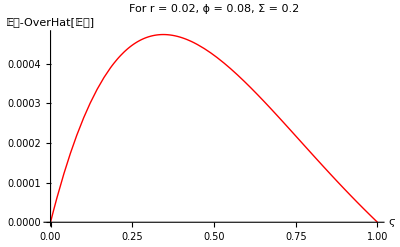

```mathematica
ClearVars;𝓇2Check = rfree+ϕ;Σ=0.2;rfree=0.02;ϕ=0.08;𝓇1Check=rfree;
(* First, show that the approximation of the (true) arithmetic return by the Campbell-Viceira approximation
   is good (or at least much better than the geometric approximation)*)
Off[NIntegrate::inumr]; (*Turn off some annoying warning messages*)
ExactMinusApproxLogExpectedPortfolioReturn = 
Plot[{𝔼𝔯CheckNInt[ϛ,Σ]-𝔼𝔯CheckCVApprox[ϛ,Σ](*,𝔼𝔯CheckNInt[ϛ,Σ]-𝔼𝔯CheckGeometric[ϛ,Σ]*)}
  ,{ϛ,0,1}
  ,AxesLabel->{"ϛ","𝔼𝔯-OverHat[𝔼𝔯]"}
  ,BaseStyle->{FontSize->14}
  ,PlotLabel->"For r = "<>ToString[rfree]<>", ϕ = "<>ToString[ϕ]<>", Σ = "<>ToString[Σ]
  ,PlotStyle->{Black,Red}
,PlotLegend->{"Campbell-Viceira"(*,"Geometric"*)}
,LegendSize->0.75
,LegendTextSpace->5
,LegendPosition->{0.,0.}
]
(*
Export["./Figures/ExactMinusApproxLogExpectedPortfolioReturn.pdf",ExactMinusApproxLogExpectedPortfolioReturn];
Export["./Figures/ExactMinusApproxLogExpectedPortfolioReturn.png",ExactMinusApproxLogExpectedPortfolioReturn,ImageSize->72 9];
Export["./Figures/ExactMinusApproxLogExpectedPortfolioReturn.svg",ExactMinusApproxLogExpectedPortfolioReturn];
Print[ExactMinusApproxLogExpectedPortfolioReturn];
On[NIntegrate::inumr];
*)
```

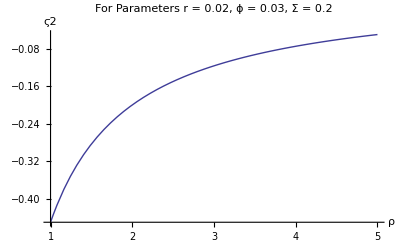

```mathematica
𝓇2Check=0.05;rfree=0.02;ϕ=𝓇2Check-rfree;Σ=0.2;
ShareVsCRRA = Plot[ϛ2OptApprox[Σ,ρ],{ρ,1,5}
,AxesLabel->{"ρ","ϛ2"}
,PlotLabel->"For Parameters r = "<>ToString[rfree]<>", ϕ = "<>ToString[ϕ]<>", Σ = "<>ToString[Σ]
,BaseStyle->{FontSize->14}
];
Export["./Figures/ShareVsCRRA.pdf",ShareVsCRRA];
Export["./Figures/ShareVsCRRA.png",ShareVsCRRA,ImageSize->72 9];
Export["./Figures/ShareVsCRRA.svg",ShareVsCRRA];
Print[ShareVsCRRA];
```

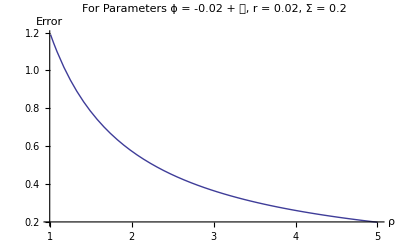

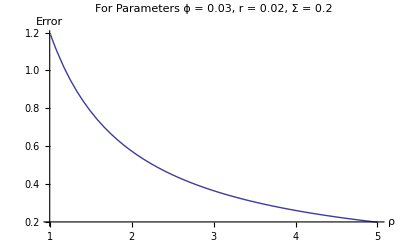

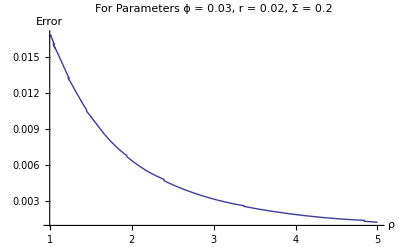

```mathematica
Off[NIntegrate::inumr]; (*Turn off some annoying warning messages*)
ShareApproxErr=Plot[{ϛ2OptExact[Σ,ρ]-ϛ2OptApprox[Σ,ρ]},{ρ,1.01,5}
,PlotLabel->"For Parameters ϕ = "<>ToString[ϕ]<>", r = "<>ToString[rfree]<>", Σ = "<>ToString[Σ]
,BaseStyle->{FontSize->14}
,AxesLabel->{"ρ","Error"}];
Export["./Figures/ShareApproxErr.pdf",ShareApproxErr];
Export["./Figures/ShareApproxErr.png",ShareApproxErr,ImageSize->72 9];
Export["./Figures/ShareApproxErr.svg",ShareApproxErr];
Print[ShareApproxErr];
On[NIntegrate::inumr];
```

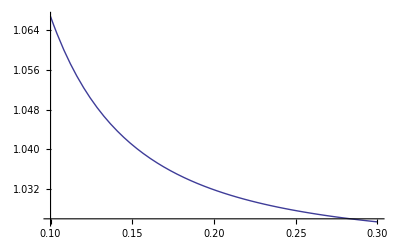

```mathematica
Print[Plot[𝔼ℜGivenOptϛ2Approx[ΣPlot,ρ=2],{ΣPlot,0.1,0.3}]];
```

```mathematica
Σ𝔯GivenΣApprox[Σ_,ρ_] := Block[{ϛ2Approx},
  ϛ2Approx=ϛ2OptApprox[Σ,ρ];
  NIntegrate[PDF[LogNormalDistribution[ϕ-(Σ^2)/2,Σ],Φtp1](ϛ2Approx Log[Φtp1]+ϛ2Approx(1-ϛ2Approx)(Σ^2)/2),{Φtp1,0,∞}]
];
```

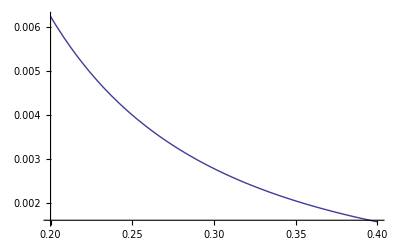

```mathematica
Print[Plot[Σ𝔯GivenΣApprox[ΣPlot,3],{ΣPlot,0.2,0.4}]];
```